```mathematica
(59-2)/4-1
```

53/4

```mathematica
(4-59)/-1-4
```

51

```mathematica
(14-4)/3-1
```

7/3

```mathematica
(-53-14)/-4-3
```

55/4

```mathematica
(51-53/4)/-1-1
```

-155/4

```mathematica
(7/3 - 51)/3-4
```

-182/9

```mathematica
(55/4-7/3)/-4-(-1)
```

-89/48

```mathematica
57/3
```

19

```mathematica
(*Function definition*)

f[x_] := (x^2 + 8);
```

```mathematica
f[8]
```

72

```mathematica
list= {1, 2, 58, 1};

(*How to run all of the values in the list through a function*)
f[list]
```

{9,12,3372,9}

```mathematica
(*How to get element at index*)
```

```mathematica
list[[1]]
```

```mathematica
1
(*How to get a sublist*)
list[[1;;3]]
```

1

{1,2,58}

```mathematica
(*How to get length of a list*)
```

```mathematica
Length[list]
```

4

```mathematica
(*How to make a for cycle*)
For[i = 1, i <= Length[list], i++, Print[list[[i]]]];
```

1

2

58

1

```mathematica
(*If statement*)
If[0<5, Print[2]; a=47, Print[5]]
```

2

47

```mathematica
dividedDiff[nodes_, values_];
```

```mathematica
newtonPoly[nodes_, values_, x_];
```

```mathematica
nodes={-2,1,4,-1,3,-4};
```

```mathematica
values= {-1, 2,59,4,24,-53};
```

(-2+dividexDiff[{1},{5}])/N

```mathematica
dividedDiff[nodes_,vals_]:=(If[Length[nodes]==1,vals[[1]],((dividedDiff[nodes[[2;;Length[nodes]]],vals[[2;;Length[nodes]]]]-dividedDiff[nodes[[1;;Length[nodes]-1]],vals[[1;;Length[nodes]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]]))]);
```

```mathematica
dividedDiff[{1,4},{5,48}]
```

43/3

```mathematica
newtonPoly[nodes_, values_, x_] := (values[[1]]+Sum[dividedDiff[nodes[[1;;n]], values[[1;;n]]]*Product[x-nodes[[i]],{i,1,n-1}], {n, 2, Length[nodes]}]);
```

```mathematica
newtonPoly[{0,1,4},{2,5,48}, x]
```

2+3 x+17/6 (-1+x) x

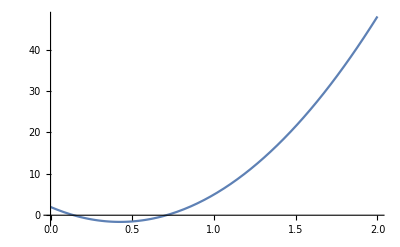

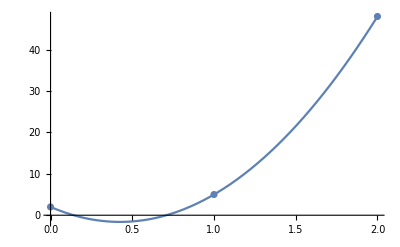

```mathematica
plotTest = Plot[newtonPoly[{0,1,2},{2,5,48}, x], {x, 0,2}]
plotTest2 =  ListPlot[{{0, 2}, {1, 5},{2, 48}}];
Show[{plotTest, plotTest2}]
```